# Artificial Neuron

## The artificial neuron is the basic building block of artificial, convolutional, and other popular neural networks, and forms the basis of most of modern deep learning.

## Modeling the Artificial Neuron

Historically, the artificial neuron is supposed to have developed from the biological neuron. Let’s try to visualise that.

Pull up a couple of images of a biological neuron:

```mathematica
bioNeuron = WebImageSearch["Neuron","Thumbnails","MaxItems"->2]
```

{-Graphics-,-Graphics-}

We can see the main parts of this structure seem to be: dendrite, axon and axon terminal.

Now let’s pull up a couple of images of an artificial neuron:

```mathematica
artificialNeuron = WebImageSearch["Artificial neuron","Thumbnails","MaxItems"->2]
```

{-Graphics-,-Graphics-}

The first image of biological neuron, and the second image of artificial neuron look similar. So let’s compare them.

```mathematica
bioNeuron[[1]] 
artificialNeuron[[2]]
```

-Graphics-

-Graphics-

So the association seems to be:
• Dendrite → Input
• Axon → Net Input
• Axon terminal → Activation (Output)

## Nuts and Bolts of the Neuron

Now let’s try to visualise what happens at each of the 3 parts identified above.

### Dendrite

The dendrites take input via a vector product. Let’s visualise vectors and their products:

```mathematica
x = RandomInteger[10,{5}]
```

{3,6,9,10,3}

```mathematica
w = RandomInteger[10,{5}]
```

{8,7,9,7,0}

```mathematica
x.w
```

146

Let’s visualise how the values of the individual vectors have changed after multiplication.

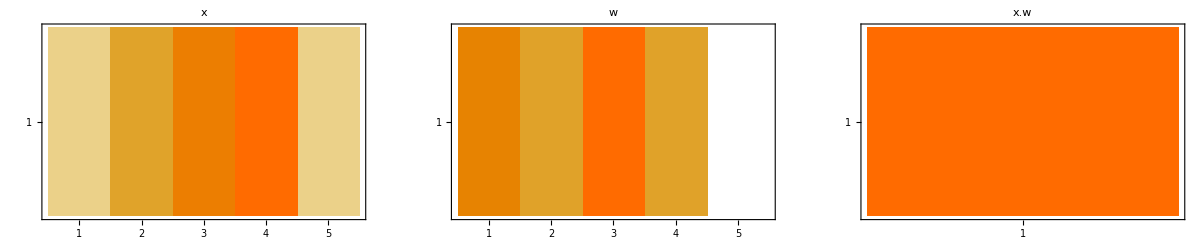

```mathematica
GraphicsRow[{MatrixPlot[{x},PlotLabel->"x"],MatrixPlot[{w},PlotLabel->"w"],MatrixPlot[{{x.w}},PlotLabel->"x.w"]}]
```

In the analogy of the biological neuron, the value of x.w tells us how intense the inputs collected from the dendrites are (by getting scaled up by the weight vector w), once they have entered the neuron. The higher the value, the more intense the input.

### Axon

Looking back at the picture of the artificial neuron, we see that this part basically sums up a lot of vector products.

```mathematica
x1 = RandomInteger[10,{5}]
w1 = RandomInteger[10,{5}]
x2 = RandomInteger[10,{5}]
w2 = RandomInteger[10,{5}]
```

{10,10,6,1,8}

{2,1,10,1,7}

{0,9,3,5,3}

{2,8,8,0,3}

```mathematica
net = x1.w1 + x2.w2
```

252

```mathematica
ImageCollage[{MatrixPlot[{x1},PlotLabel->"x_1"],MatrixPlot[{x2},PlotLabel->"x_2"],MatrixPlot[{w1},PlotLabel->"w_1"],MatrixPlot[{w2},PlotLabel->"w_2"],MatrixPlot[{{net}},PlotLabel->"net"]}]
```

-Graphics-

The value of the activation (output) of the neuron tells us how intense a signal the neuron is sending to the subsequent neurons in the network.

### Axon Terminal

This part uses something called an activation function. An activation function introduces non-linearity into the values of the neuron. Let’s look at some activation functions.

Plot the sigmoid function:

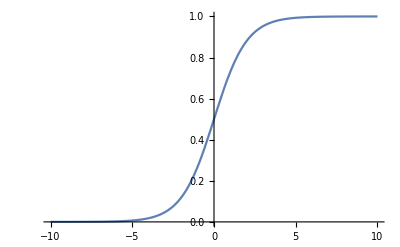

```mathematica
Plot[LogisticSigmoid[x],{x,-10,10}]
```

Plot the tanh function:

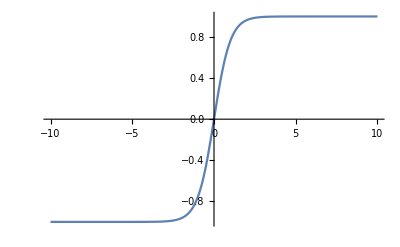

```mathematica
Plot[Tanh[x],{x,-10,10}]
```

The tanh functions seems to be steeper than sigmoid, and is hence closer to the discontinuous function plotted below.

The above functions are basically differentiable approximations for the following function:

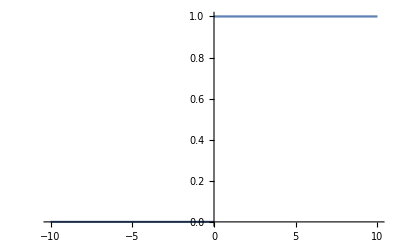

```mathematica
Plot[Piecewise[{{0,x<0},{1,x>0}}],{x,-10,10}]
```

The above function is useful for binary classification (0 being one class, 1 being another). We use the above functions instead because they are differentiable and allow us to use our good friend calculus.

We’ll look at some other popular activation functions:

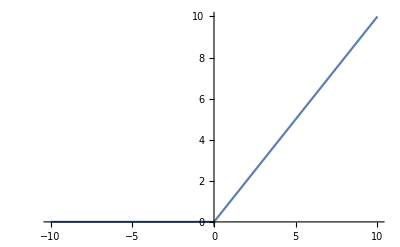

```mathematica
Plot[Ramp[x],{x,-10,10}]
```

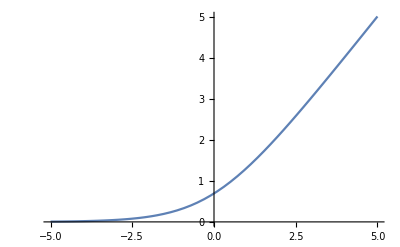

```mathematica
Plot[Log[1 + Exp[x]],{x,-5,5}]
```

## Applications

You know what’s cooler and more powerful than a single neuron? A network of neurons! Also known as a neural network.

### Feedforward Neural Network

Let’s visualise a typical neural network called a feedforward neural network:

```mathematica
Graph[Flatten[Join[Table[x->y,{x,1,3},{y,4,7}],Table[x->y,{x,4,7},{y,8,9}]]],PlotTheme->"Detailed",VertexSize->0.4,VertexShape->-Graphics-,DirectedEdges->True]
```

-Graphics-

From the above graph, we can easily see how each neuron takes inputs at its dendrites, accumulates them into its axon, and outputs activations at its terminal. An edge between 2 neurons represents flow of information between them.

### Convolutional Neural Network

Now we’ll see a CNN, which is very popular for image processing.

First let’s see what a convolution is:

[f*g](t) = ∫_(-∞)^∞ f(τ)g(t-τ)dτ

That looks intimidating! Let’s look at a visualisation of that:

```mathematica
Animate[Block[{g1=PDF[NormalDistribution[],n],g2=PDF[NormalDistribution[t,2],n],g3},g3=g1*g2;
Show[Plot[{g1,g2},{n,-5,5}],Plot[g3,{n,-5,5},Filling->Axis,PlotStyle->Red]]],{t,-5,5}]
```

The output in red is the convolution of the 2 functions shown in blue and yellow. Convolution is basically a product of 2 functions. Feel free to play around with the slider and understand what is going on.

Now let’s see how convolution is used inside a CNN. Let’s make a random matrix first:

```mathematica
matrix = RandomInteger[10,{5,5}]
matrix//MatrixForm
```

{{3,3,8,7,5},{5,6,2,9,0},{9,7,6,9,0},{8,6,9,1,4},{7,1,6,7,8}}

(3 | 3 | 8 | 7 | 5
5 | 6 | 2 | 9 | 0
9 | 7 | 6 | 9 | 0
8 | 6 | 9 | 1 | 4
7 | 1 | 6 | 7 | 8)

I am initializing the convolution matrix randomly here for purposes of visualization. See the animation below for details.

```mathematica
convolution=RandomInteger[10,{3,3}]
convolution//MatrixForm
```

{{4,7,4},{7,5,8},{5,5,6}}

(4 | 7 | 4
7 | 5 | 8
5 | 5 | 6)

In reality, the convolution is calculated by running a tiny kernel (the 3x3 square frame below) over the input matrix, and mapping the set of numbers within the kernel to a part of the output (the scalar within the frame in the output).

```mathematica
ListAnimate[Flatten[Table[Grid[matrix,Frame->{None,None,{{{x,x+2},{y,y+2}}->True}}],{x, 3}, {y, 3}]]]
ListAnimate[Flatten[Table[Grid[convolution,Frame->{None,None,{{{x,x},{y,y}}->True}}],{x, 3}, {y, 3}]]]
```

One of the most important features of a CNN is that when the kernel moves around over the input, it always uses the same weights to map that region of input to the output.

Apart from the convolution, a CNN has basically the same structure as a feedforward neural network visualised above.

## Further Explorations

• Backpropagation
• Training a neural network
• Recurrent neural network, Long Short Term Memory (LSTM)

## Authorship Information

Rohan Saxena

23rd June, 2017

saxenarohan97@gmail.com